Optimal creation of entanglement using a two-qubit gate

B. Kraus and J. I. Cirac PRA (2001)
Notebook: Óscar Amaro

Introduction
In this notebook we reproduce figure 1.

## Figure 0

{{Cos[α],0,0,-ⅈ Sin[α]},{0,Cos[α],-ⅈ Sin[α],0},{0,-ⅈ Sin[α],Cos[α],0},{-ⅈ Sin[α],0,0,Cos[α]}}

{Cos[α],0,0,-ⅈ Sin[α]}

-(Cos[α]^2 Log[Cos[α]^2])/Log[2]-(Log[Sin[α]^2] Sin[α]^2)/Log[2]

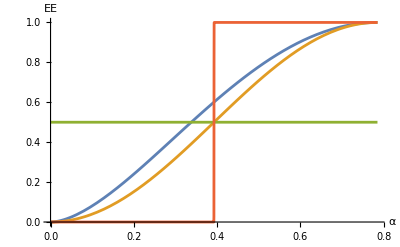

```mathematica
Clear[ERme,ERps,α,ψ1,ψ2,σx,Ud,maxEE]

σx=PauliMatrix[1];

Ud=Cos[α] IdentityMatrix[4]- I Sin[α] KroneckerProduct[σx,σx]
ψ=Ud.{1,0,0,0}

(* this expression looks similar to sin^2 but is less symmetric*)
maxEE=-Cos[α]^2 Log2[Cos[α]^2]-Sin[α]^2 Log2[Sin[α]^2]

Plot[{maxEE,Sin[2α]^2,0.5,(Tanh[(α-π/8)10000]+1)/2},{α,0,π/4},AxesLabel->{"α","EE"}]
```

## Figure 1

3/16 (3-2 Cos[4 α]-Cos[4 α]^2)

1/2 (1-Cos[4 α]^2)

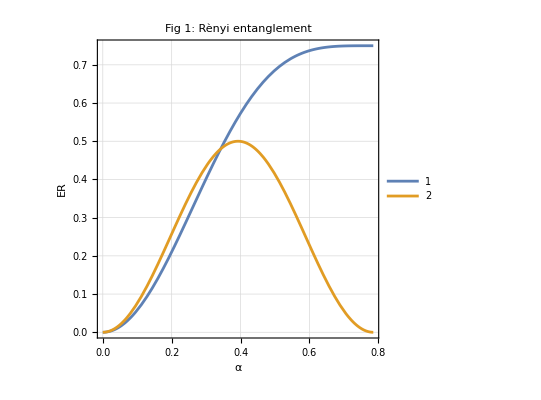

{α→1/4 ArcCos[1/5]}

```mathematica
Clear[ERme,ERps,α,ψ1,ψ2]

(* maximally entangled input state *) 
ψ1={1,0,0,1}/Sqrt[2];

(* produce state*)
ψ1={0,1,0,0};

ERme=3/16(3-2Cos[4α]-Cos[4α]^2)
ERps=1/2(1-Cos[4α]^2)
Plot[{ERme,ERps},{α,0,π/4},Frame->True,AspectRatio->1,FrameLabel->{"α","ER"},FrameStyle->Directive[Thick,Black],GridLines->Automatic,PlotLegends->{"1","2"},PlotLabel->"Fig 1: Rènyi entanglement"]
(Solve[ERps==ERme,α][[3]]//Normal)/.{C[1]->0}
```